```mathematica
(* For jet structure see: lornetz_factor_limit.nb *)
(* NOW: See gamma_jet.nb for complete new jet structure *)
```

```mathematica
(* Set constants and fluid values at r0 *)
```

```mathematica
M=3*msun
rl=G*M/c^2
r0=10*rl
Gam0=2
theta0deg=30
theta0=theta0deg*Pi/180
nu=3/4
sigma0=1000
B0=10^(15)*(r0/rl)^(-1)
rho0=B0^2/(8*Pi*c^2)/sigma0
n0=rho0/mb
```

5.967×10^33

442966.

4.42966×10^6

2

30

π/6

3/4

1000

1.×10^14

442.709

2.64498×10^26

```mathematica
(* Set jet solution *)
```

```mathematica
Gamff=Gam0*(r/r0)^(1-nu/2)
Gammhd=sigma0
Gam=1/(1/Gamff+1/Gammhd)
theta=theta0*(r/r0)^(-nu/2)
gdet=r^2*Sin[theta]
gdet0=gdet//.{r->r0}
rho=rho0/(Gam/Gam0*gdet/gdet0)
nden=rho/mb
R=r*Sin[theta]
z=r*Cos[theta]
s=2/nu
MM=0.2
T=(z/R)^(-(2-nu))
Bphihat=Bphihat00*(-nu*s*MM*R^(nu-2)*T^((nu-1)/nu))
fun=Bphihat//.{r->r0}
sols=Solve[fun==-B0,Bphihat00]
Bphihat0=sols[[1,1,2]]
Bphihat=Bphihat0*(-nu*s*MM*R^(nu-2)*T^((nu-1)/nu))
```

0.000140297 r^(5/8)

1000

1/(1/1000+7127.74/r^(5/8))

162.7/r^(3/8)

r^2 Sin[162.7/r^(3/8)]

9.81096×10^12

(8.68681×10^15 (1/1000+7127.74/r^(5/8)) Csc[162.7/r^(3/8)])/r^2

(5.18995×10^39 (1/1000+7127.74/r^(5/8)) Csc[162.7/r^(3/8)])/r^2

r Sin[162.7/r^(3/8)]

r Cos[162.7/r^(3/8)]

8/3

0.2

1/(Cot[162.7/r^(3/8)]^(5/4))

-(0.4 Bphihat00)/((1/(Cot[162.7/r^(3/8)]^(5/4)))^(1/3) (r Sin[162.7/r^(3/8)])^(5/4))

-5.88551×10^-9 Bphihat00

{{Bphihat00→1.69909×10^22}}

1.69909×10^22

-(6.79635×10^21)/((1/(Cot[162.7/r^(3/8)]^(5/4)))^(1/3) (r Sin[162.7/r^(3/8)])^(5/4))

```mathematica
(* equipartition temperature for just baryons *)
```

```mathematica
Te=Bphihat^2/(8*Pi)/(2*kb*nden)
Plot[Te,{r,r0,100*rl}]
```

(1.28239×10^18 r^2 Sin[162.7/r^(3/8)])/((1/1000+7127.74/r^(5/8)) (1/(Cot[162.7/r^(3/8)]^(5/4)))^(2/3) (r Sin[162.7/r^(3/8)])^(5/2))

-Graphics-

```mathematica
(* field strength *)
```

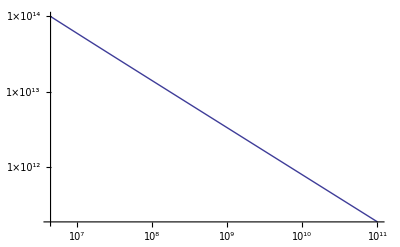

```mathematica
LogLogPlot[-Bphihat,{r,r0,10^(11)}]
```

```mathematica
(* rest-mass density in baryons *)
```

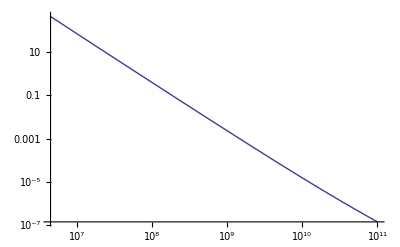

```mathematica
LogLogPlot[rho,{r,r0,10^(11)}]
```

```mathematica
(* number density of baryons *)
```

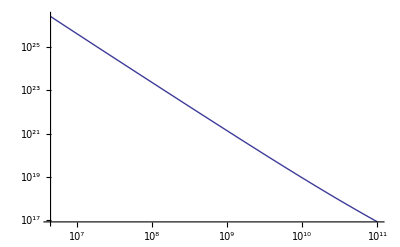

```mathematica
LogLogPlot[nden,{r,r0,10^(11)}]
```

```mathematica
(* Lorentz factor *)
```

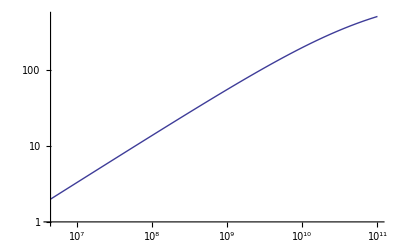

```mathematica
LogLogPlot[Gam,{r,r0,10^(11)}]
```

```mathematica
(* Half-opening angle in degrees *)
```

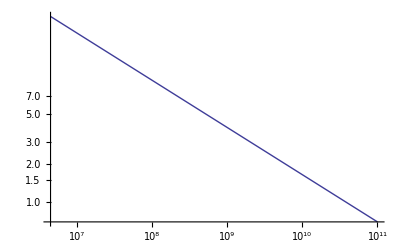

```mathematica
LogLogPlot[180/Pi*theta,{r,r0,10^(11)}]
```

```mathematica
(* Choose radius to solve equations at *)
```

```mathematica
myrconst={r->10^11}
```

{r→100000000000}

```mathematica
(* Find equipartition temperature in reconnection layer *)
```

```mathematica
Pbaryon=rho*Tg*kb/mb
Pe=Pbaryon
urad=arad*Tg^4
Prad=arad*Tg^4/3
Ppairs=arad*Tg^4*7/12*Exp[-me*c^2/(kb*Tg)]
(*Ppairs=arad*Tg^4*7/12*)
Pg=Prad+Ppairs+Pbaryon+Pe
Ug=(Ppairs+Prad)/(4/3-1)+(Pe+Pbaryon)/(5/3-1)
Pb=Bphihat^2/(8*Pi)
eqT=(Pg==Pb)//.myrconst
sols=FindRoot[eqT,{Tg,10^9},WorkingPrecision->20]
(*myTg=sols[[4,1,2]]*)
myTg=sols[[1,2]]
```

(7.16576×10^23 (1/1000+7127.74/r^(5/8)) Tg Csc[162.7/r^(3/8)])/r^2

(7.16576×10^23 (1/1000+7127.74/r^(5/8)) Tg Csc[162.7/r^(3/8)])/r^2

7.56683×10^-15 Tg^4

2.52228×10^-15 Tg^4

4.41399×10^-15 ⅇ^(-5.92968×10^9/Tg) Tg^4

2.52228×10^-15 Tg^4+4.41399×10^-15 ⅇ^(-5.92968×10^9/Tg) Tg^4+(1.43315×10^24 (1/1000+7127.74/r^(5/8)) Tg Csc[162.7/r^(3/8)])/r^2

3 (2.52228×10^-15 Tg^4+4.41399×10^-15 ⅇ^(-5.92968×10^9/Tg) Tg^4)+(2.14973×10^24 (1/1000+7127.74/r^(5/8)) Tg Csc[162.7/r^(3/8)])/r^2

(1.83786×10^42)/((1/(Cot[162.7/r^(3/8)]^(5/4)))^(2/3) (r Sin[162.7/r^(3/8)])^(5/2))

22.9119 Tg+2.52228×10^-15 Tg^4+4.41399×10^-15 ⅇ^(-5.92968×10^9/Tg) Tg^4==1.39004×10^21

FindRoot::precw: The precision of the argument function (22.9119\ Tg + « 24 »\ Tg^4 + 4.41399×10^-15\ ⅇ^-« 21 »/Tg\ Tg^4 == « 23 ») is less than WorkingPrecision (20.).

{Tg→8.6122110452867736111×10^8}

8.6122110452867736111×10^8

```mathematica
(* Look at pressures at equipartition temperature *)
```

```mathematica
Pbaryon//.{Tg->myTg}//.myrconst
Prad//.{Tg->myTg}//.myrconst
Ppairs//.{Tg->myTg}//.myrconst
Pg//.{Tg->myTg}//.myrconst
Pb//.{Tg->myTg}//.myrconst
```

9.86611×10^9

1.38756×10^21

2.48363×10^18

1.39004×10^21

1.39004×10^21

```mathematica
(* Timescale for photon diffusion (cooling timescale) across layer vs transit time through layer = light crossing time *)
```

```mathematica
(*
2 regimes:
1) optically thin inefficient cooling
2) very optically thick
*)
(* dominate cooling: synchrotron and Compton *)
```

```mathematica
(* Use temperature from above *)
```

```mathematica
newTgconst={Tg->myTg}
```

{Tg→8.6122110452867736111×10^8}

```mathematica
(* Set number densities of pairs, total electrons+positrons, and skin depths *)
```

```mathematica
npairs=(7/4*arad*Tg^4/(kb*Tg))*Exp[-me*c^2/(kb*Tg)]
ndentot=nden+npairs//.newTgconst//.myrconst
omegape=Sqrt[4*Pi*ndentot*q^2/me]
omegapi=Sqrt[4*Pi*nden*q^2/mp]
de=c/omegape
di=c/omegapi
j1=c*B0/(4*Pi*c)*omegape
j2=q*nden*vd
```

95.9076 ⅇ^(-5.92968×10^9/Tg) Tg^3

6.26605×10^25

4.46541×10^17

9.48399×10^22 √(((1/1000+7127.74/r^(5/8)) Csc[162.7/r^(3/8)])/r^2)

6.71366×10^-8

(3.16104×10^-13)/(√(((1/1000+7127.74/r^(5/8)) Csc[162.7/r^(3/8)])/r^2))

3.55346×10^30

(2.49268×10^30 (1/1000+7127.74/r^(5/8)) vd Csc[162.7/r^(3/8)])/r^2

```mathematica
(* Look at number densities *)
```

```mathematica
npairs//.newTgconst//.myrconst
nden//.newTgconst//.myrconst
```

6.26605×10^25

8.29721×10^16

```mathematica
(* Compute Larmor radius *)
```

```mathematica
Ee=3/2*kb*Tg//.{Tg->myTg}
ve=Sqrt[Ee*2/me]//.myrconst
wge=q*(-Bphihat)/(me*c)
Rl=ve/wge//.myrconst
```

1.78363×10^-7

1.9789×10^10

(1.19528×10^29)/((1/(Cot[162.7/r^(3/8)]^(5/4)))^(1/3) (r Sin[162.7/r^(3/8)])^(5/4))

6.01998×10^-9

```mathematica
(* compute ptical depth to electron scattering within Petschek layer *)
tau=sigmat*ndentot*de
```

2.79838×10^-6

```mathematica
(* Compare annihilation time to plasma time to see if pairs included as charge carriers for plasma frequency *)
```

```mathematica
Tann=1/(n*sigmat*c)
omegap=Sqrt[4*Pi*n*q^2/me]
Tp=2*Pi/omegap
myn=Solve[Tann==Tp,n][[1,1,2]]
myn*me*mp/me
paireden=myn*me*c^2
```

(5.01449×10^13)/n

56411. √n

0.000111382/(√n)

2.02685×10^35

3.39016×10^11

1.65941×10^29

```mathematica
(* Obtain classical critical field strength *)
```

```mathematica
Solve[paireden==Bit^2/(8*Pi),Bit]
```

{{Bit→-2.04219×10^15},{Bit→2.04219×10^15}}

```mathematica
(* estimate quantum correction *)
```

```mathematica
2*10^15/137.
```

1.45985×10^13

```mathematica
(* Compare number density with classical electron density *)
```

```mathematica
1/(4*Pi/3*radiuse^3)
```

1.06729×10^37

```mathematica
(* so similar *)
```

```mathematica
(* Estimate resistivity *)
```

```mathematica
(* q nden v_d = q j = q E/etaprime *)
```

```mathematica
(*
etaprime=me/(nden*q^2)/taucoll
eta=etaprime*c^2/(4*Pi)
lambdamfp=
eta=de^2/(lambdamfp)*ve
*)
```

```mathematica
(* or: eE = F = v_d/c urad sigmaT *)
```

```mathematica
(* check units *)
```

```mathematica
E0=MMM*LL^2/S^2
(LL/S/(1/S))^2*E0/LL^3*LL^2/(LL/S)
```

(LL^2 MMM)/S^2

(LL^2 MMM)/S

```mathematica
(* Get SP and Spitzer resistivity and corresponding SP lengths across layer *)
```

```mathematica
(*etaprime=urad*sigmat/(ndentot*q^2*c)//.newTgconst//.myrconst*)
eta=(c/omegape)^2/me*urad*sigmat/c//.newTgconst//.myrconst
etaspitzer=c*radiuse*(kb*Tg/(me*c^2))^(-3/2)*20//.newTgconst//.myrconst
L=R//.newTgconst//.myrconst
Va=c*(-Bphihat)/Sqrt[rho*c^2+Ug+Pg+Bphihat^2]//.newTgconst//.myrconst
deltasp=Sqrt[L*eta/Va]//.newTgconst//.myrconst
deltaspitzer=Sqrt[L*etaspitzer/Va]//.newTgconst//.myrconst
```

0.457019

3.05212

1.22005×10^9

2.78452×10^10

0.141508

0.365691

```mathematica
(* Sweet Parker optical depth across layer and along layer *)
```

```mathematica
tausp=sigmat*ndentot*deltasp
tauL=sigmat*ndentot*L
```

5.8983

5.08538×10^10

```mathematica
(* Compare photon diffusion time across layer and transit time along layer *)
```

```mathematica
TdiffacrossSP = tausp*deltasp/c//.newTgconst//.myrconst
Ttransit=L/Va//.newTgconst//.myrconst
```

2.78412×10^-11

0.0438154

```mathematica
(* So photons leak out and cool layer before transiting fluid is heated *)
```

```mathematica
(* Compute lindquist number *)
```

```mathematica
Lindquist=L*Va/eta//.newTgconst//.myrconst
```

7.43348×10^19

```mathematica
(* Compare size of Petschek and SP layers *)
```

```mathematica
de/deltasp
```

4.74437×10^-7

```mathematica
(* So SP much larger as is normal *)
```

```mathematica
(* Check resistivity from Plasma book *)
```

```mathematica
Tev=kb*Tg/ergPmev*10^6
lnL=20
etaprimebook=10^(-14)*lnL*(Tev)^(-3/2)//.newTgconst//.myrconst
etabook=etaprimebook*c^2/(4*Pi)
```

0.0000861765 Tg

20

9.89178×10^-21

0.707467

```mathematica
(* So similar to Spitzer we wrote down *)
```

```mathematica
(* Compute optical depth to baryon-electron scattering *)
```

```mathematica
Tb=10^4
sigmac=sigmat/(kb*Tb/(me*c^2))^2
tau=L*nden*sigmac//.myrconst
```

10000

2.33891×10^-13

2.36768×10^13

```mathematica
(* So for any reasonable temperature baryons and electrons are significantly coupled due to high density still *)
```